```mathematica
Clear["Global`*"]
```

# Origin

## Cory Aitchison - February 2022

Consider an ansatz of a weighted average of u0 + some function that satisfies the DE near the origin.

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

### Long data

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
fdata = Interpolation[data];
```

## Rationale

By looking at the numerical solution, we know that we want a solution that looks like

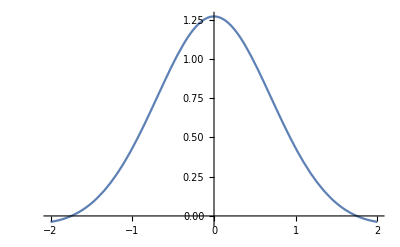

```mathematica
Plot[fdata[x], {x,-2,2}]
```

and the 4th derivative looks like:

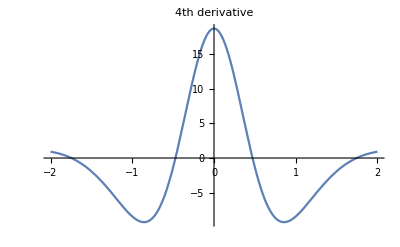

```mathematica
Plot[-de2[fdata][x] - de3[fdata][x] /. param /. estimates, {x,-2,2}, PlotLabel-> "4th derivative"]
```

The solution looks quite similar to a Gaussian near the origin; what about the 4th derivative?

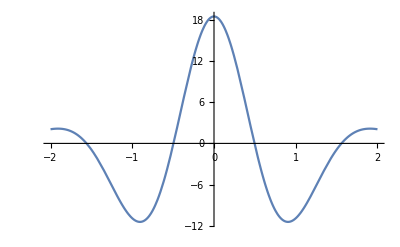

```mathematica
Plot[de1[x |-> 1.23Exp[- 1.12x^2]][x] /. param, {x,-2,2}]
```

This looks qualitatively quite similar. 

So what if we combine a Gaussian with our original ansatz u0?
i.e. use a weighting scheme so that near the origin the Gaussian is relevant, and far from x = 0 the u0 dominates.

Note that the cos/cosh does not look the same:

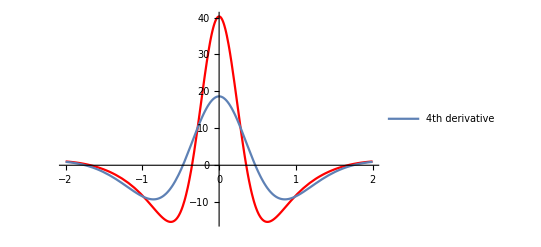

```mathematica
Show[Plot[de1[u[0]][x]/.param/.estimates, {x,-2,2}, PlotRange->All, PlotStyle->Red], Plot[-de2[fdata][x] - de3[fdata][x] /. param /. estimates, {x,-2,2}, PlotLegends-> {"4th derivative"}]]
```

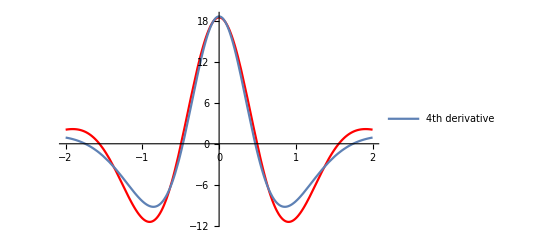

```mathematica
Show[Plot[de1[x |-> 1.23Exp[- 1.12x^2]][x] /. param, {x,-2,2}, PlotRange->All, PlotStyle->Red], Plot[-de2[fdata][x] - de3[fdata][x] /. param /. estimates, {x,-2,2}, PlotLegends-> {"4th derivative"}]]
```

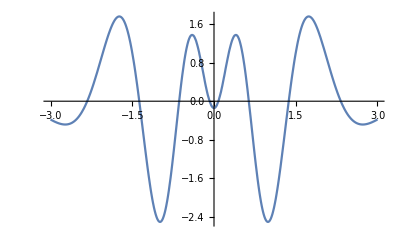

```mathematica
Plot[de1[x |-> 1.23Exp[- 1.12x^2]][x] +de2[fdata][x] + de3[fdata][x] /. param /. estimates, {x,-3,3}, PlotRange->All]
```

## Examples

### Weighting 1

First try weighting using [1, exp(-x^2)]. The rational behind this is that by using just exponential functions, we retain that gaussian shape. We also want the weighting to decay faster than 1/cosh(x) so that the u0 term dominates in the tails.

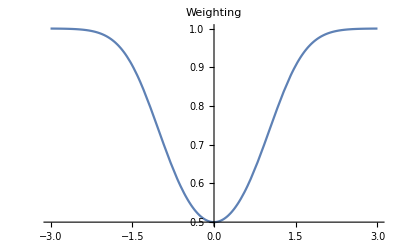

```mathematica
Plot[1/ (Exp[-x^2] + 1), {x,-3,3}, PlotLabel->Weighting]
```

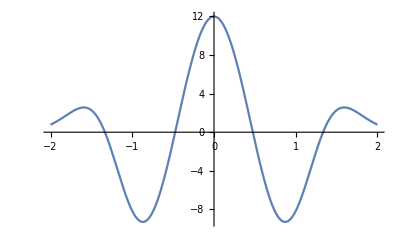

```mathematica
Plot[de1[x |-> Exp[- 2x^2]/(1 + Exp[-x^2])][x] /. param, {x,-2,2}]
```

Even with the added weighting, this does look quite similar to the result we want

```mathematica
ex1[x_] := (u[0][x]+ 0.82Exp[-1.874x^2]) /(1 +0.81Exp[-x^2]);
```

```mathematica
(*ex1[x_] := (u[0][x] + u[1][x]+ 1.05Exp[-1.874x^2]) /(1 +0.81 Exp[-x^2]) /. answer[1];*)
```

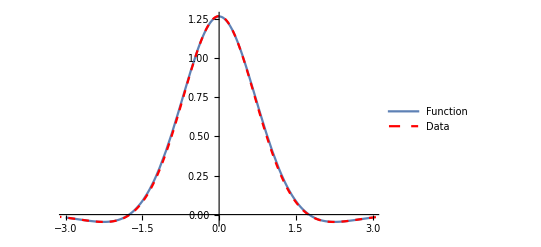

```mathematica
Show[Plot[ex1[x]/. param /. estimates, {x,-3,3}, PlotLegends->{Function}], ListLinePlot[data,  PlotRange->{{-3,3}, {-3,3}}, PlotStyle->{Red, Dashed}, PlotLegends->{Data}]]
```

It also fits well to the solution in both the peak and the tails (as expected)

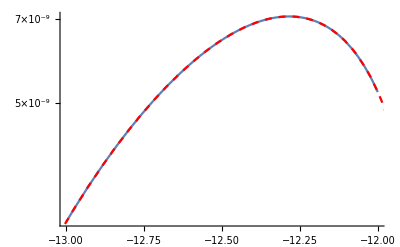

```mathematica
Show[LogPlot[ex1[x] /.param /. estimates, {x,-13, -12}],ListLogPlot[data,  PlotRange->{{-13,-11}, Automatic}, PlotStyle->{Red, Dashed}, Joined->True]]
```

What about the DE?

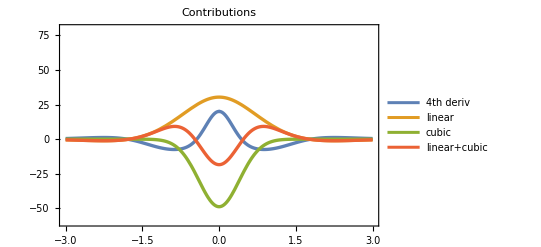

```mathematica
Plot[{
de1[ex1][x] /. param /. estimates,
de2[ex1][x] /. param /. estimates,
de3[ex1][x] /. param /. estimates,
de2[ex1][x] + de3[ex1][x] /. param /. estimates
}, {x,-3,3},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, Frame->True, PlotLabel->Contributions]
```

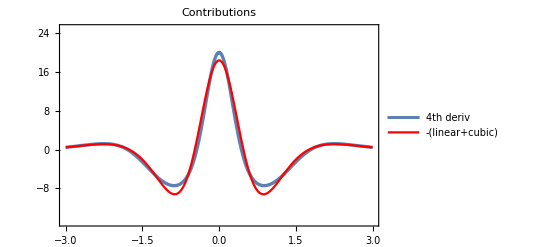

```mathematica
Plot[{
de1[ex1][x] /. param /. estimates,
-(de2[ex1][x] + de3[ex1][x]) /. param /. estimates
}, {x,-3,3},PlotLegends-> {"4th deriv", "-(linear+cubic)"}, PlotStyle->{Thickness[0.006], {Blue, Red}}, PlotRange->{Automatic, {-15, 25}}, Frame->True, PlotLabel->Contributions]
```

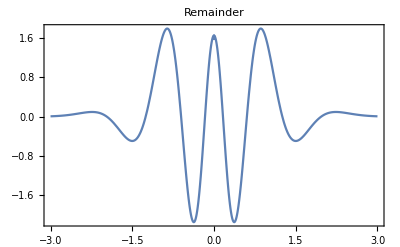

```mathematica
Plot[de1[ex1][x] + de2[ex1][x] + de3[ex1][x] /. param /. estimates, {x,-3,3}, Frame -> True, PlotLabel->"Remainder", PlotRange->All]
```

This is a much smaller remainder than just the u0 ansatz!

#### Minimizing remainder

Perhaps we can minimise the remainder by fine-tuning the coefficients near the peak:

```mathematica
my2[x_] := (u[0][x]+(a1 b1) Exp[-(a2+b2)x^2]) /(1 + b1 Exp[-b2 x^2]);
Manipulate[Plot[de1[my2][x] + de2[my2][x] + de3[my2][x]/. {a1 -> A1, a2 -> A2, b1 -> B1, b2 -> B2}/. param /. estimates, {x,-4,4}, Frame -> True, PlotLegends->{"Remainder"}, PlotRange->All], {{A1, 1},0,3}, {{A2, 0.874}, 0, 3}, {{B1, 0.81},0,3},{{B2, 1},0,3}]
```

#### Taylor Expanding Remainder

```mathematica
ex2[x_] := (u[0][x]+ν Exp[-(1 + η)x^2]) /(1 + ν Exp[-x^2]);
Chop[Series[ex2''''[x] + 4 σ^4 ex2[x] + Γ ex2[x]^3 /. param /.estimates, {x,0,2}]]
```

1/(1.+ν)^3 12. (-0.0944985-2.75311 ν+2. η ν+η^2 ν-1.92388 ν^2+2. η ν^2+2. η^2 ν^2+η^2 ν^3)-1/(1.+ν)^4 60. (4.65721+1.91073 ν+0.794281 η ν+3. η^2 ν+η^3 ν+2.96167 ν^2-4.94231 η ν^2+6. η^2 ν^2+3. η^3 ν^2+2.99414 ν^3-6.53659 η ν^3+3. η^2 ν^3+3. η^3 ν^3-0.8 η ν^4+η^3 ν^4) x^2+O[x]^3

```mathematica
NSolve[%1046 == 0, {ν, η}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ν→-1.79429,η→0.631446},{ν→-1.27789-1.88716 ⅈ,η→0.53943+0.394534 ⅈ},{ν→-1.27789+1.88716 ⅈ,η→0.53943-0.394534 ⅈ},{ν→-1.21099,η→-0.757692},{ν→-1.,η→-1.66354×10^15},{ν→-1.,η→-3.64043×10^16},{ν→0.0000390146,η→-50.2513},{ν→0.0570976-0.521472 ⅈ,η→-2.3464-0.960741 ⅈ},{ν→0.0570976+0.521472 ⅈ,η→-2.3464+0.960741 ⅈ},{ν→5.65571,η→0.424842}}

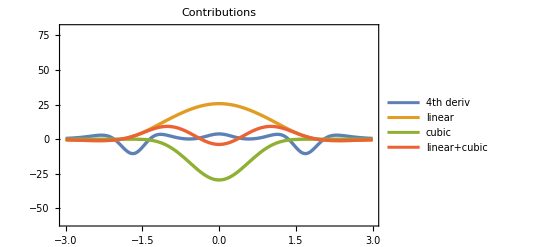

```mathematica
Plot[{
de1[ex2][x] /. %1048[[-1]]/. param /. estimates,
de2[ex2][x] /. %1048[[-1]]/. param /. estimates,
de3[ex2][x] /. %1048[[-1]]/. param /. estimates,
de2[ex2][x] + de3[ex2][x] /. %1048[[-1]]/. param /. estimates
}, {x,-3,3},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, Frame->True, PlotLabel->Contributions]
```

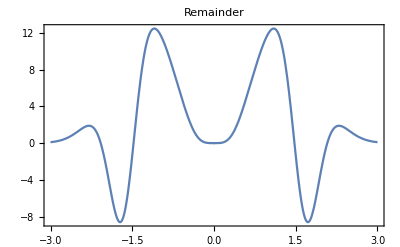

```mathematica
Plot[de1[ex2][x] + de2[ex2][x] + de3[ex2][x] /. %1048[[-1]]/. param /. estimates, {x,-3,3}, Frame -> True, PlotLabel->"Remainder", PlotRange->All]
```

### Cosh instead of gaussian

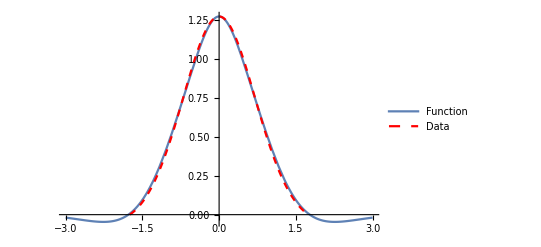

```mathematica
ex4[x_] := u[0][x](1-Exp[-x^2])+1.27Exp[- x^2]Sech[1.7x];Show[Plot[ex4[x]/. param /. estimates, {x,-3,3}, PlotLegends->{Function}], ListLinePlot[data,  PlotRange->{{-2,2}, {0,3}}, PlotStyle->{Red, Dashed}, PlotLegends->{Data}]]
```

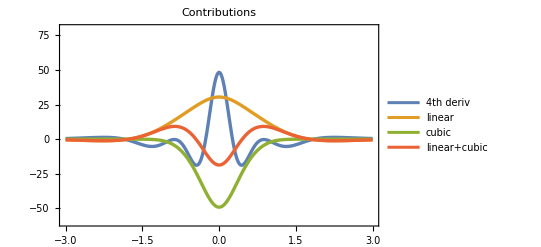

```mathematica
Plot[{
de1[ex4][x] /. param /. estimates,
de2[ex4][x] /. param /. estimates,
de3[ex4][x] /. param /. estimates,
de2[ex4][x] + de3[ex4][x] /. param /. estimates
}, {x,-3,3},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, Frame->True, PlotLabel->Contributions]
```

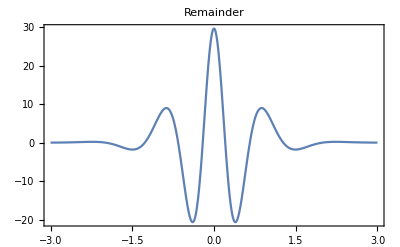

```mathematica
Plot[de1[ex4][x] + de2[ex4][x] + de3[ex4][x] /. param /. estimates, {x,-3,3}, Frame -> True, PlotLabel->"Remainder", PlotRange->All]
```

```mathematica
ex3a[x_] := u[0][x](1-Exp[-a x^2])+1.27Exp[-(a+b)x^2];
Manipulate[Plot[de1[ex3a][x] + de2[ex3a][x] + de3[ex3a][x]/. {a -> A, b -> B}/. param /. estimates, {x,-4,4}, Frame -> True, PlotLegends->{"Remainder"}, PlotRange->All], {{A, 1}, 0, 2}, {{B,1},0,2}]
```

### Weighting 2

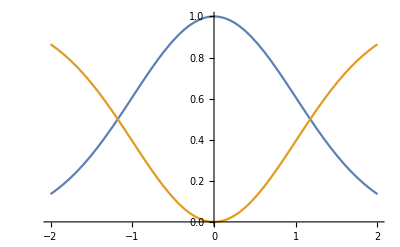

```mathematica
Plot[{Exp[-0.5x^2], 1-Exp[-0.5x^2]}, {x,-2,2}]
```

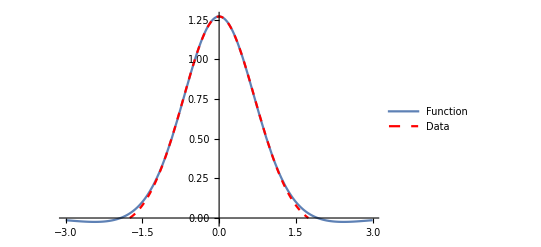

```mathematica
ex3[x_] := u[0][x](1-Exp[-0.146x^2])+1.27Exp[-(1.092+0.146)x^2];Show[Plot[ex3[x]/. param /. estimates, {x,-3,3}, PlotLegends->{Function}], ListLinePlot[data,  PlotRange->{{-2,2}, {0,3}}, PlotStyle->{Red, Dashed}, PlotLegends->{Data}]]
```

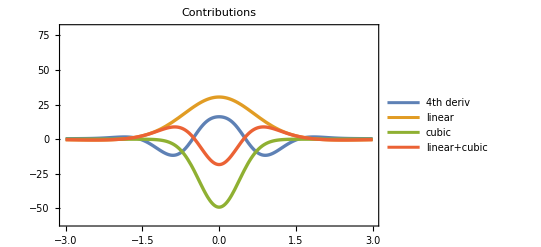

```mathematica
Plot[{
de1[ex3][x] /. param /. estimates,
de2[ex3][x] /. param /. estimates,
de3[ex3][x] /. param /. estimates,
de2[ex3][x] + de3[ex1][x] /. param /. estimates
}, {x,-3,3},PlotLegends-> {"4th deriv", "linear", "cubic","linear+cubic"}, PlotStyle->{Thickness[0.006]}, PlotRange->{Automatic, {-60, 80}}, Frame->True, PlotLabel->Contributions]
```

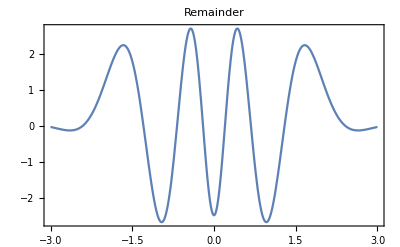

```mathematica
Plot[de1[ex3][x] + de2[ex3][x] + de3[ex3][x] /. param /. estimates, {x,-3,3}, Frame -> True, PlotLabel->"Remainder", PlotRange->All]
```

```mathematica
ex3a[x_] := u[0][x](1-Exp[-a x^2])+1.27Exp[-(a+b)x^2];
Manipulate[Plot[de1[ex3a][x] + de2[ex3a][x] + de3[ex3a][x]/. {a -> A, b -> B}/. param /. estimates, {x,-4,4}, Frame -> True, PlotLegends->{"Remainder"}, PlotRange->All], {{A, 1}, 0, 2}, {{B,1},0,2}]
```

```mathematica
NSolve[D[ex3[x],{x,4}]  ==0/. param /.estimates]
```

$Aborted

```mathematica
LDE[ex3] + NDE[ex3]
```

1.27 (18.3917 ⅇ^(-1.238 x^2)-91.0758 ⅇ^(-1.238 x^2) x^2+37.584 ⅇ^(-1.238 x^2) x^4)+(-0.255792 ⅇ^(-0.146 x^2)+0.149383 ⅇ^(-0.146 x^2) x^2-0.00726995 ⅇ^(-0.146 x^2) x^4) (A Cos[x σ] Sech[x σ]+B Csch[x σ] Sin[x σ])+4 σ^4 (1.27 ⅇ^(-1.238 x^2)+(1-ⅇ^(-0.146 x^2)) (A Cos[x σ] Sech[x σ]+B Csch[x σ] Sin[x σ]))+Γ (1.27 ⅇ^(-1.238 x^2)+(1-ⅇ^(-0.146 x^2)) (A Cos[x σ] Sech[x σ]+B Csch[x σ] Sin[x σ]))^3+4 (-0.255792 ⅇ^(-0.146 x^2) x+0.0248971 ⅇ^(-0.146 x^2) x^3) (B σ Cos[x σ] Csch[x σ]-B σ Coth[x σ] Csch[x σ] Sin[x σ]-A σ Sech[x σ] Sin[x σ]-A σ Cos[x σ] Sech[x σ] Tanh[x σ])+6 (0.292 ⅇ^(-0.146 x^2)-0.085264 ⅇ^(-0.146 x^2) x^2) (-2 B σ^2 Cos[x σ] Coth[x σ] Csch[x σ]-A σ^2 Cos[x σ] Sech[x σ]-B σ^2 Csch[x σ] Sin[x σ]+B (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3) Sin[x σ]+2 A σ^2 Sech[x σ] Sin[x σ] Tanh[x σ]+A Cos[x σ] (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2))+1.168 ⅇ^(-0.146 x^2) x (-B σ^3 Cos[x σ] Csch[x σ]+3 B σ Cos[x σ] (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3)+3 B σ^3 Coth[x σ] Csch[x σ] Sin[x σ]+B (-σ^3 Coth[x σ]^3 Csch[x σ]-5 σ^3 Coth[x σ] Csch[x σ]^3) Sin[x σ]+A σ^3 Sech[x σ] Sin[x σ]+3 A σ^3 Cos[x σ] Sech[x σ] Tanh[x σ]-3 A σ Sin[x σ] (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2)+A Cos[x σ] (5 σ^3 Sech[x σ]^3 Tanh[x σ]-σ^3 Sech[x σ] Tanh[x σ]^3))+(1-ⅇ^(-0.146 x^2)) (4 B σ^4 Cos[x σ] Coth[x σ] Csch[x σ]+4 B σ Cos[x σ] (-σ^3 Coth[x σ]^3 Csch[x σ]-5 σ^3 Coth[x σ] Csch[x σ]^3)+A σ^4 Cos[x σ] Sech[x σ]+B σ^4 Csch[x σ] Sin[x σ]-6 B σ^2 (σ^2 Coth[x σ]^2 Csch[x σ]+σ^2 Csch[x σ]^3) Sin[x σ]+B (σ^4 Coth[x σ]^4 Csch[x σ]+18 σ^4 Coth[x σ]^2 Csch[x σ]^3+5 σ^4 Csch[x σ]^5) Sin[x σ]-4 A σ^4 Sech[x σ] Sin[x σ] Tanh[x σ]-6 A σ^2 Cos[x σ] (-σ^2 Sech[x σ]^3+σ^2 Sech[x σ] Tanh[x σ]^2)-4 A σ Sin[x σ] (5 σ^3 Sech[x σ]^3 Tanh[x σ]-σ^3 Sech[x σ] Tanh[x σ]^3)+A Cos[x σ] (5 σ^4 Sech[x σ]^5-18 σ^4 Sech[x σ]^3 Tanh[x σ]^2+σ^4 Sech[x σ] Tanh[x σ]^4))

```mathematica
Series[%1340 /. estimates /. param, {x,0,4}]// Chop
```

-2.46517+76.3745 x^2-418.087 x^4+O[x]^5